```mathematica
(*1.4a*)
```

```mathematica
(*Analytically compute the eigenvalues, λ​1 and λ2​​, of M​σ and confirm that they constitute a complex conjugate pair*)
f[x,y,σ]=σ+1*x[t]+3*y[t];
g[x,y,σ]=-2*x[t]+σ-1*y[t];
M = {{σ+1,3}, {-2,σ-1}}; (*from the eqs above*)
eigenVal = Eigenvalues[M]
```

{-ⅈ √5+σ,ⅈ √5+σ}

```mathematica
(*1.4b*)
(*Solve the dynamical system analytically for the initial values x(0)=u and y(0)=v*)
```

```mathematica
x1[t_] = {x[t],y[t]};
dynS = x1'[t] == M.x1[t];
solution = DSolve[dynS,{x,y},t];
x1[t_,x0_,y0_,σ_] = {x[t],y[t]}/.solution[[1]]/.{C[1]->u, C[2]->v}
```

{(3 ⅇ^(t σ) v Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) u (5 Cos[√5 t]+√5 Sin[√5 t]),-(2 ⅇ^(t σ) u Sin[√5 t])/(√5)+1/5 ⅇ^(t σ) v (5 Cos[√5 t]-√5 Sin[√5 t])}

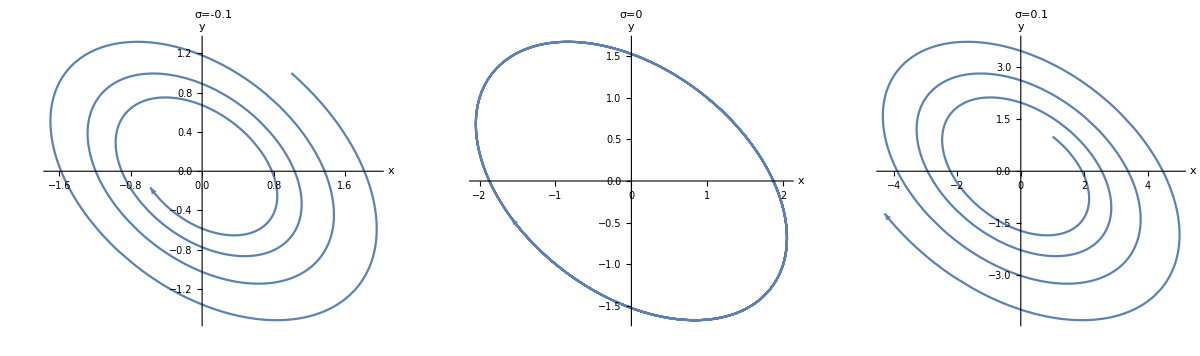

```mathematica
(*1.4c*)
(*Plot in three figures representative trajectories for σ=−1/10,σ=0 and σ=1/10*)
f1 = x1[t,1,1,-0.1];
f1[[1]];
p1=ParametricPlot[x1[t,1,1,-0.1]/.u->1/.v->1,{t,0,10},AxesLabel->{x,y}, PlotLabel->"σ=-0.1"] /.Line -> Arrow;
p2=ParametricPlot[x1[t,1,1,0]/.u->1/.v->1,{t,0,10},AxesLabel->{x,y}, PlotLabel->"σ=0"] /.Line -> Arrow;
p3=ParametricPlot[x1[t,1,1,0.1]/.u->1/.v->1,{t,0,10},AxesLabel->{x,y}, PlotLabel->"σ=0.1"] /.Line -> Arrow;
GraphicsRow[{p1,p2,p3}]
```

```mathematica
(*1.4d*)
(*When σ=0 the system has an invariant orbit in the form of an ellipse. Analytically compute the period of the ellips0*)
Solve[x1[0,u,v,0]==x1[t,u,v,0],t]
```

{{t→ConditionalExpression[(2 π C[1])/(√5), C[1]∈ℤ]}}

```mathematica
(*e) Analytically calculate the length ratio between the major and minor axes of the ellipse*)
t0 = 1;
xyVal = x1[t,1,1,0]/.u->1/.v->1;
(*Circle equation r^2=x^2+y^2*)
radius=Sqrt[(xyVal[[1]])^2+(xyVal[[2]])^2];
a=FindMaximum[radius,{t,t0}];
b=FindMinimum[radius,{t,t0}];
ratio=a b;
ratio[[1,1]](*The ratio is equivalent with 1+sqrt(5)2*)
```

1.39095

```mathematica
(*1.4f*)
(*Analytically calculate the direction of the major ellipse axis in the (x,y) plane*)
(*As in the previous task where σ=0. We get t-position from the major ellipse and normalize.*)
dirMajor=xyVal/. {u->1,v->1,σ->0,a⟦2⟧⟦1⟧};
Normalize[dirMajor]
```

{0.850651,-0.525731}